```mathematica
Get[FileNameJoin[{NotebookDirectory[],"cudamemcpy.m"}]]
```

/Users/abduld/.gvm/pkgsets/go1.8.1/global/src/github.com/rai-project/microbench/results/cudaMemcpy_plot.png

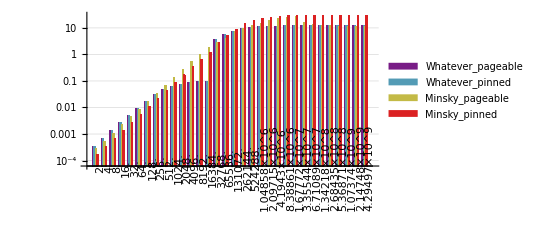

```mathematica
makeChart[data_]:=BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"machine"]->Lookup[val,"bytes_per_second"]/1024^3]],data],First]],ChartLabels->{Placed[First/@Keys[data],Automatic,Rotate[#,90 Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,2},PlotTheme->"Grid",ScalingFunctions->"Log",ChartStyle->"Rainbow"]; 
makeChart[groupedData]
```

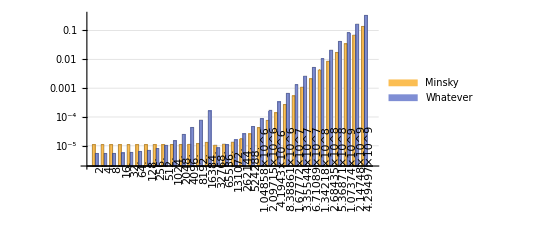

```mathematica
makeChart[data_]:=BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"machine"]->Lookup[val,"cpu_time"]/10^9]],data],First]],ChartLabels->{Placed[First/@Keys[data],Automatic,Rotate[#,90 Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]; 
makeChart[groupedData]
```

```mathematica
groupedData
```

<|{2.}→{<|name→CUDAMemcpyToGPU/1,iterations→102407,real_time→6832.03,cpu_time→6805.21,time_unit→ns,bytes_per_second→293892.,bytes→2.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/1,iterations→182908,real_time→3819.33,cpu_time→3819.3,time_unit→ns,bytes_per_second→523656.,bytes→2.,machine→Whatever|>},{4.}→{<|name→CUDAMemcpyToGPU/2,iterations→103061,real_time→6949.15,cpu_time→6929.81,time_unit→ns,bytes_per_second→577217.,bytes→4.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/2,iterations→183075,real_time→3796.61,cpu_time→3796.59,time_unit→ns,bytes_per_second→1.05358×10^6,bytes→4.,machine→Whatever|>},{8.}→{<|name→CUDAMemcpyToGPU/3,iterations→101191,real_time→6920.13,cpu_time→6900.77,time_unit→ns,bytes_per_second→1.15929×10^6,bytes→8.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/3,iterations→183644,real_time→3805.68,cpu_time→3805.66,time_unit→ns,bytes_per_second→2.10213×10^6,bytes→8.,machine→Whatever|>},{16.}→{<|name→CUDAMemcpyToGPU/4,iterations→101157,real_time→6797.44,cpu_time→6794.74,time_unit→ns,bytes_per_second→2.35476×10^6,bytes→16.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/4,iterations→182710,real_time→3813.05,cpu_time→3813.02,time_unit→ns,bytes_per_second→4.19614×10^6,bytes→16.,machine→Whatever|>},{32.}→{<|name→CUDAMemcpyToGPU/5,iterations→103044,real_time→6787.29,cpu_time→6786.38,time_unit→ns,bytes_per_second→4.71533×10^6,bytes→32.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/5,iterations→183129,real_time→3818.15,cpu_time→3818.11,time_unit→ns,bytes_per_second→8.3811×10^6,bytes→32.,machine→Whatever|>},{64.}→{<|name→CUDAMemcpyToGPU/6,iterations→103102,real_time→6855.71,cpu_time→6854.18,time_unit→ns,bytes_per_second→9.33737×10^6,bytes→64.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/6,iterations→181676,real_time→3836.04,cpu_time→3836.03,time_unit→ns,bytes_per_second→1.66839×10^7,bytes→64.,machine→Whatever|>},{128.}→{<|name→CUDAMemcpyToGPU/7,iterations→101514,real_time→6921.2,cpu_time→6921.11,time_unit→ns,bytes_per_second→1.84941×10^7,bytes→128.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/7,iterations→180861,real_time→3864.07,cpu_time→3864.04,time_unit→ns,bytes_per_second→3.31259×10^7,bytes→128.,machine→Whatever|>},{256.}→{<|name→CUDAMemcpyToGPU/8,iterations→100922,real_time→6937.3,cpu_time→6937.26,time_unit→ns,bytes_per_second→3.69022×10^7,bytes→256.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/8,iterations→179989,real_time→3876.59,cpu_time→3876.58,time_unit→ns,bytes_per_second→6.60377×10^7,bytes→256.,machine→Whatever|>},{512.}→{<|name→CUDAMemcpyToGPU/9,iterations→100644,real_time→6935.16,cpu_time→6935.08,time_unit→ns,bytes_per_second→7.38276×10^7,bytes→512.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/9,iterations→179801,real_time→3898.81,cpu_time→3898.8,time_unit→ns,bytes_per_second→1.31323×10^8,bytes→512.,machine→Whatever|>},{1024.}→{<|name→CUDAMemcpyToGPU/10,iterations→100408,real_time→6840.69,cpu_time→6840.55,time_unit→ns,bytes_per_second→1.49696×10^8,bytes→1024.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/10,iterations→174584,real_time→4061.86,cpu_time→4061.84,time_unit→ns,bytes_per_second→2.52102×10^8,bytes→1024.,machine→Whatever|>},{2048.}→{<|name→CUDAMemcpyToGPU/11,iterations→101771,real_time→6881.77,cpu_time→6879.24,time_unit→ns,bytes_per_second→2.97707×10^8,bytes→2048.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/11,iterations→162765,real_time→4305.27,cpu_time→4305.26,time_unit→ns,bytes_per_second→4.75697×10^8,bytes→2048.,machine→Whatever|>},{4096.}→{<|name→CUDAMemcpyToGPU/12,iterations→100638,real_time→6961.8,cpu_time→6958.36,time_unit→ns,bytes_per_second→5.88645×10^8,bytes→4096.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/12,iterations→156798,real_time→4485.83,cpu_time→4485.8,time_unit→ns,bytes_per_second→9.13104×10^8,bytes→4096.,machine→Whatever|>},{8192.}→{<|name→CUDAMemcpyToGPU/13,iterations→94877,real_time→7366.96,cpu_time→7366.29,time_unit→ns,bytes_per_second→1.11209×10^9,bytes→8192.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/13,iterations→132783,real_time→5314.92,cpu_time→5314.91,time_unit→ns,bytes_per_second→1.54133×10^9,bytes→8192.,machine→Whatever|>},{16384.}→{<|name→CUDAMemcpyToGPU/14,iterations→83573,real_time→8275.52,cpu_time→8273.75,time_unit→ns,bytes_per_second→1.98024×10^9,bytes→16384.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/14,iterations→100464,real_time→6875.22,cpu_time→6875.2,time_unit→ns,bytes_per_second→2.38306×10^9,bytes→16384.,machine→Whatever|>},{32768.}→{<|name→CUDAMemcpyToGPU/15,iterations→66403,real_time→10600.1,cpu_time→10543.3,time_unit→ns,bytes_per_second→3.10794×10^9,bytes→32768.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/15,iterations→74525,real_time→9096.6,cpu_time→9096.56,time_unit→ns,bytes_per_second→3.60224×10^9,bytes→32768.,machine→Whatever|>},{65536.}→{<|name→CUDAMemcpyToGPU/16,iterations→47225,real_time→14830.6,cpu_time→14824.2,time_unit→ns,bytes_per_second→4.42089×10^9,bytes→65536.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/16,iterations→52553,real_time→13345.8,cpu_time→13345.8,time_unit→ns,bytes_per_second→4.91063×10^9,bytes→65536.,machine→Whatever|>},{131072.}→{<|name→CUDAMemcpyToGPU/17,iterations→42372,real_time→16481.5,cpu_time→16466.3,time_unit→ns,bytes_per_second→7.96×10^9,bytes→131072.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/17,iterations→30937,real_time→22629.1,cpu_time→22629.1,time_unit→ns,bytes_per_second→5.7922×10^9,bytes→131072.,machine→Whatever|>},{262144.}→{<|name→CUDAMemcpyToGPU/18,iterations→27772,real_time→25181.7,cpu_time→25170.5,time_unit→ns,bytes_per_second→1.04147×10^10,bytes→262144.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/18,iterations→17790,real_time→39338.7,cpu_time→39338.7,time_unit→ns,bytes_per_second→6.66377×10^9,bytes→262144.,machine→Whatever|>},{524288.}→{<|name→CUDAMemcpyToGPU/19,iterations→18289,real_time→38299.8,cpu_time→38283.3,time_unit→ns,bytes_per_second→1.36949×10^10,bytes→524288.,machine→Minsky|>,<|name→CUDAMemcpyToGPU/19,iterations→9670,real_time→72453.,cpu_time→72453.,time_unit→ns,bytes_per_second→7.23625×10^9,bytes→524288.,machine→Whatever|>},{1.04858×10^6}→{<|name→CUDAMemcpyToGPU/20,iterations→10477,real_time→66926.9,cpu_time→66785.7,time_unit→ns,bytes_per_second→1.57006×10^10,bytes→1.04858×10^6,machine→Minsky|>,<|name→CUDAMemcpyToGPU/20,iterations→5066,real_time→138238.,cpu_time→138237.,time_unit→ns,bytes_per_second→7.58532×10^9,bytes→1.04858×10^6,machine→Whatever|>},{2.09715×10^6}→{<|name→CUDAMemcpyToGPU/21,iterations→6871,real_time→101963.,cpu_time→101882.,time_unit→ns,bytes_per_second→2.05841×10^10,bytes→2.09715×10^6,machine→Minsky|>,<|name→CUDAMemcpyToGPU/21,iterations→3164,real_time→221330.,cpu_time→221329.,time_unit→ns,bytes_per_second→9.47528×10^9,bytes→2.09715×10^6,machine→Whatever|>},{4.1943×10^6}→{<|name→CUDAMemcpyToGPU/22,iterations→4069,real_time→172171.,cpu_time→172042.,time_unit→ns,bytes_per_second→2.43795×10^10,bytes→4.1943×10^6,machine→Minsky|>,<|name→CUDAMemcpyToGPU/22,iterations→1804,real_time→388092.,cpu_time→388091.,time_unit→ns,bytes_per_second→1.08075×10^10,bytes→4.1943×10^6,machine→Whatever|>},{8.38861×10^6}→{<|name→CUDAMemcpyToGPU/23,iterations→2242,real_time→312416.,cpu_time→312284.,time_unit→ns,bytes_per_second→2.68621×10^10,bytes→8.38861×10^6,machine→Minsky|>,<|name→CUDAMemcpyToGPU/23,iterations→934,real_time→751405.,cpu_time→751401.,time_unit→ns,bytes_per_second→1.1164×10^10,bytes→8.38861×10^6,machine→Whatever|>},{1.67772×10^7}→{<|name→CUDAMemcpyToGPU/24,iterations→1182,real_time→592832.,cpu_time→592691.,time_unit→ns,bytes_per_second→2.83069×10^10,bytes→1.67772×10^7,machine→Minsky|>,<|name→CUDAMemcpyToGPU/24,iterations→459,real_time→1.52745×10^6,cpu_time→1.52743×10^6,time_unit→ns,bytes_per_second→1.09839×10^10,bytes→1.67772×10^7,machine→Whatever|>},{3.35544×10^7}→{<|name→CUDAMemcpyToGPU/25,iterations→357,real_time→1.95895×10^6,cpu_time→1.9585×10^6,time_unit→ns,bytes_per_second→1.71327×10^10,bytes→3.35544×10^7,machine→Minsky|>,<|name→CUDAMemcpyToGPU/25,iterations→203,real_time→3.44302×10^6,cpu_time→3.443×10^6,time_unit→ns,bytes_per_second→9.7457×10^9,bytes→3.35544×10^7,machine→Whatever|>},{6.71089×10^7}→{<|name→CUDAMemcpyToGPU/26,iterations→150,real_time→4.67861×10^6,cpu_time→4.67669×10^6,time_unit→ns,bytes_per_second→1.43497×10^10,bytes→6.71089×10^7,machine→Minsky|>,<|name→CUDAMemcpyToGPU/26,iterations→103,real_time→6.80149×10^6,cpu_time→6.80145×10^6,time_unit→ns,bytes_per_second→9.86684×10^9,bytes→6.71089×10^7,machine→Whatever|>},{1.34218×10^8}→{<|name→CUDAMemcpyToGPU/27,iterations→69,real_time→1.00954×10^7,cpu_time→1.00914×10^7,time_unit→ns,bytes_per_second→1.33002×10^10,bytes→1.34218×10^8,machine→Minsky|>,<|name→CUDAMemcpyToGPU/27,iterations→52,real_time→1.35204×10^7,cpu_time→1.35204×10^7,time_unit→ns,bytes_per_second→9.92708×10^9,bytes→1.34218×10^8,machine→Whatever|>},{2.68435×10^8}→{<|name→CUDAMemcpyToGPU/28,iterations→33,real_time→2.09077×10^7,cpu_time→2.09047×10^7,time_unit→ns,bytes_per_second→1.28409×10^10,bytes→2.68435×10^8,machine→Minsky|>,<|name→CUDAMemcpyToGPU/28,iterations→26,real_time→2.70671×10^7,cpu_time→2.7067×10^7,time_unit→ns,bytes_per_second→9.91744×10^9,bytes→2.68435×10^8,machine→Whatever|>},{5.36871×10^8}→{<|name→CUDAMemcpyToGPU/29,iterations→16,real_time→4.26205×10^7,cpu_time→4.2587×10^7,time_unit→ns,bytes_per_second→1.26064×10^10,bytes→5.36871×10^8,machine→Minsky|>,<|name→CUDAMemcpyToGPU/29,iterations→13,real_time→5.43638×10^7,cpu_time→5.43636×10^7,time_unit→ns,bytes_per_second→9.87556×10^9,bytes→5.36871×10^8,machine→Whatever|>},{1.07374×10^9}→{<|name→CUDAMemcpyToGPU/30,iterations→8,real_time→8.66338×10^7,cpu_time→8.66024×10^7,time_unit→ns,bytes_per_second→1.23985×10^10,bytes→1.07374×10^9,machine→Minsky|>,<|name→CUDAMemcpyToGPU/30,iterations→6,real_time→1.10705×10^8,cpu_time→1.10704×10^8,time_unit→ns,bytes_per_second→9.69919×10^9,bytes→1.07374×10^9,machine→Whatever|>},{2.14748×10^9}→{<|name→CUDAMemcpyToGPU/31,iterations→4,real_time→1.77169×10^8,cpu_time→1.77102×10^8,time_unit→ns,bytes_per_second→1.21257×10^10,bytes→2.14748×10^9,machine→Minsky|>,<|name→CUDAMemcpyToGPU/31,iterations→3,real_time→2.28927×10^8,cpu_time→2.28925×10^8,time_unit→ns,bytes_per_second→9.38071×10^9,bytes→2.14748×10^9,machine→Whatever|>},{4.29497×10^9}→{<|name→CUDAMemcpyToGPU/32,iterations→2,real_time→3.68271×10^8,cpu_time→3.68163×10^8,time_unit→ns,bytes_per_second→1.16659×10^10,bytes→4.29497×10^9,machine→Minsky|>,<|name→CUDAMemcpyToGPU/32,iterations→2,real_time→4.74405×10^8,cpu_time→4.74403×10^8,time_unit→ns,bytes_per_second→9.05341×10^9,bytes→4.29497×10^9,machine→Whatever|>}|>

```mathematica
BarChart[groupedData]
```

BarChart::ldata: <|{1.,1000.,1.}→{<|name→SGEMM/1000/1/1,iterations→85174,real_time→8229.36,cpu_time→8232.09,time_unit→ns,K→1.,M→1000.,N→1.,key→SMTAll|>,«1»,<|«1»|>,<|name→SGEMM/1000/1/1,iterations→86774,real_time→8059.92,«3»,M→1000.,N→1.,key→NoSMT8|>,<|name→SGEMM/1000/1/1,iterations→86109,real_time→8087.76,cpu_time→8090.34,time_unit→ns,K→1.,M→1000.,N→1.,key→NoSMT16|>},«88»,{«1»}→{«1»}|> is not a valid dataset or list of datasets.

BarChart[<|{1.,1000.,1.}→{<|name→SGEMM/1000/1/1,iterations→85174,real_time→8229.36,cpu_time→8232.09,time_unit→ns,K→1.,M→1000.,N→1.,key→SMTAll|>,<|name→SGEMM/1000/1/1,iterations→70553,5,N→1.,key→SMT16|>,<|1|>,<|1|>,<|name→SGEMM/1000/1/1,iterations→86109,real_time→8087.76,cpu_time→8090.34,time_unit→ns,K→1.,M→1000.,N→1.,key→NoSMT16|>},88,1|>]
 |  |  |  |

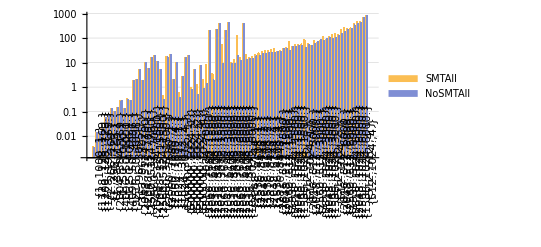

```mathematica
data=Take[groupedData,UpTo[100]];
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"cpu_time"]/10^6]],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```

```mathematica
makeChart[data_]:=BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key->AssociationThread[Lookup[val,"key"]->Lookup[val,"cpu_time"]/10^6]],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90 Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"];
```

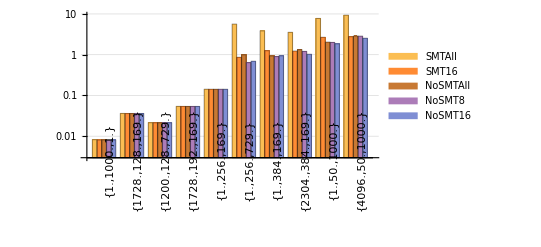

```mathematica
makeChart[data]
```

```mathematica
2560*7680*1500
```

29491200000

```mathematica
Dataset[groupedData[{500000.0,512.0,1.0}]]
```

Dataset[<>]

## AMD64 Speedup by turning off SMT

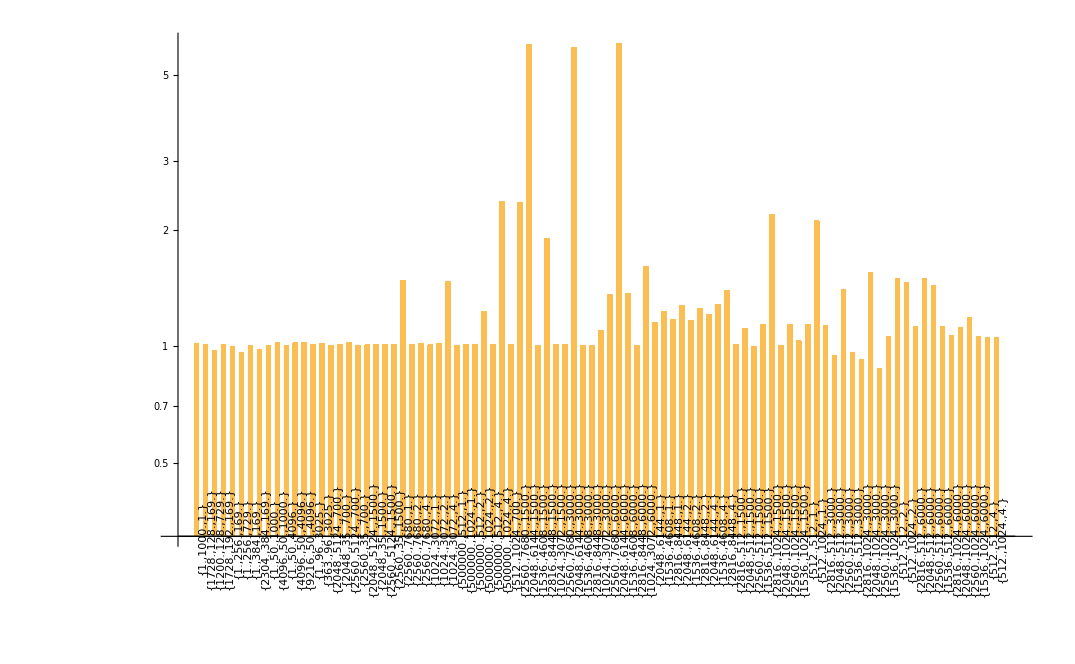

```mathematica
data=Take[groupedData,UpTo[100]];
divide[{a_,b_}]:=a/b;
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key-><|"Speedup"->divide[Lookup[val,"cpu_time"]]|>],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```

## Minsky Speedup by turning off SMT

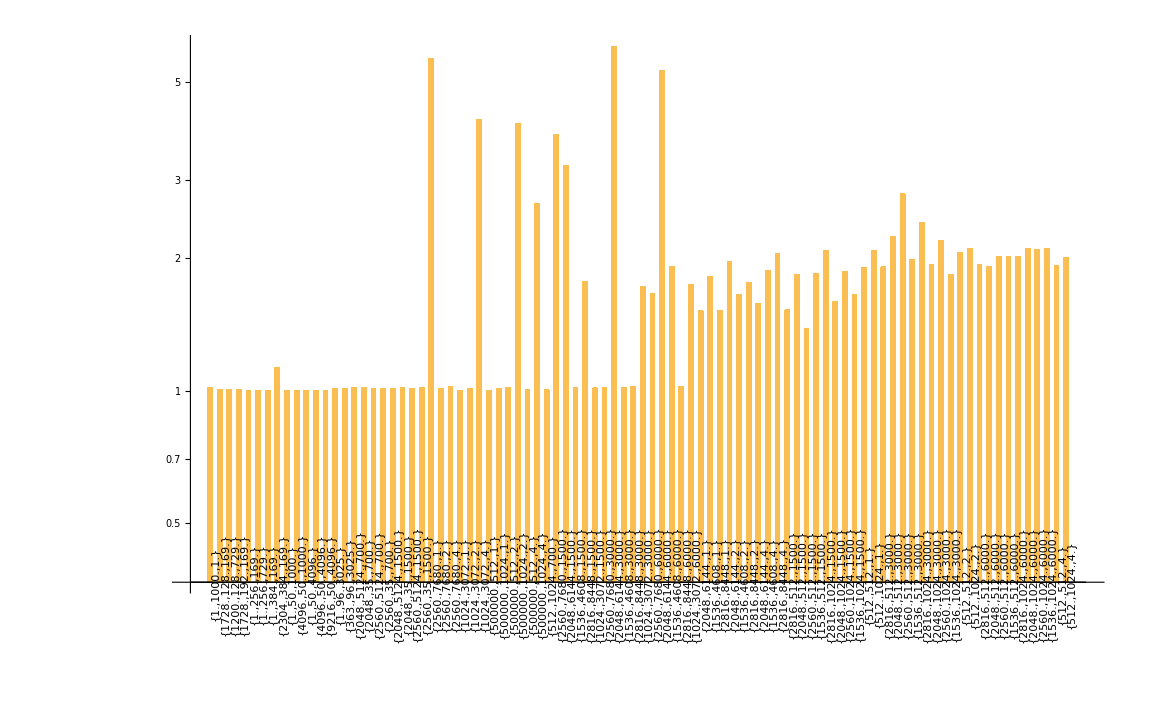

```mathematica
data=Take[groupedData,UpTo[100]];
divide[{a_,b_}]:=a/b;
BarChart[Association[SortBy[KeyValueMap[Function[{key,val},key-><|"Speedup"->divide[Lookup[val,"cpu_time"]]|>],data],Fold[Times,1,First[#]]&]],ChartLabels->{Placed[Keys[data],Automatic,Rotate[#,90Degree]&],None},ChartLegends->Automatic,BarSpacing->{Automatic,1},PlotTheme->"Grid",ScalingFunctions->"Log"]
```